## Sequential dynamics and NF fit

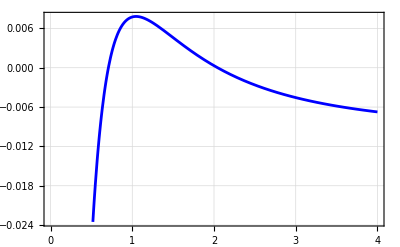

```mathematica
eval=Thread[{ka,kb,α,β,γ,da,db,dc}->{2.8,0.8,0.25,-0.4,-0.01,3,15,0.000001}];
j={{-ka,0,1},{0,-kb,1},{α,β,γ}};
jd=j-k^2DiagonalMatrix[{da,db,0}];
Plot[Eigenvalues[jd/.eval][[3]],{k,0,4},Frame->True,GridLines->Automatic,PlotStyle->Blue]
```

```mathematica
τ=12;
T=400;
period=120;
{x0,xL}={0,6Pi};
θ=1;
```

```mathematica
f[x_,t_,period_]:=UnitStep[x-(2Pi) (Quotient[t,period]+1)]
```

```mathematica
ListAnimate[Table[Plot[f[x,t,period],{x,x0,xL}],{t,0,T,5}]]
```

#### Parameter α changes with the function f taken above so that pattern can form only on domain (0, 2π) first followed by next 2π domain and so on.

```mathematica
period=120;
```

```mathematica
eqn={1/τ D[a[t,x],{t,1}]==c[t,x]-ka a[t,x]+da D[a[t,x],{x,2}]-10a[t,x]^3,1/τ D[b[t,x],{t,1}]==c[t,x]-kb b[t,x]+db D[b[t,x],{x,2}]-b[t,x]^3,1/τ D[c[t,x],{t,1}]==α (1-f[x,t,period])a[t,x]+β b[t,x]+γ c[t,x]-c[t,x]^3+dc D[c[t,x],{x,2}]}/.eval;
```

```mathematica
ic={a[0,x]==0,b[0,x]==0.001(Sum[RandomReal[{0,1}]Cos[i x],{i,10}])(*Cos[7/6x]*),c[0,x]==0};
bc={Derivative[0,1][a][t,x0]==0,Derivative[0,1][a][t,xL]==0,Derivative[0,1][b][t,x0]==0,Derivative[0,1][b][t,xL]==0,Derivative[0,1][c][t,x0]==0,Derivative[0,1][c][t,xL]==0};
```

```mathematica
{asol,bsol,csol}=NDSolveValue[{eqn,ic,bc},{a,b,c},{t,0,T},{x,x0,xL}];
```

```mathematica
ListAnimate[Table[Plot[{asol[t,x],bsol[t,x](*,csol[t,x]*)},{x,x0,xL},PlotRange->{-0.04,0.04}],{t,0,T,10}]]
```

#### Eigenfunctions

```mathematica
feig1[x_]:=UnitStep[x-2Pi]
```

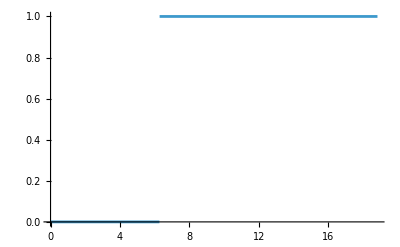

```mathematica
Plot[feig1[x],{x,0,6Pi}]
```

```mathematica
eig1=NDEigensystem[{-ka a[x]+c[x]+da a''[x],-kb b[x]+c[x]+db b''[x],α(1-feig1[x]) a[x]+β b[x]+γ c[x]}/.eval,{a[x],b[x],c[x]},{x,0,xL},7];
```

```mathematica
{s,w}={1.635Pi,2Pi};
feig2[x_]:=UnitStep[-x+s]+UnitStep[x-w-s]
```

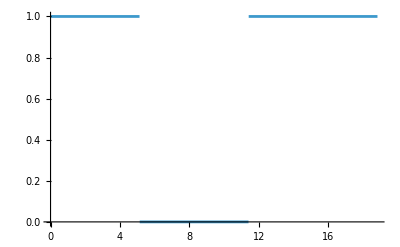

```mathematica
Plot[feig2[x],{x,x0,xL}]
```

```mathematica
eig2=NDEigensystem[{-ka a[x]+c[x]+da a''[x],-kb b[x]+c[x]+db b''[x],α(1-feig2[x]) a[x]+β b[x]+γ c[x]}/.eval,{a[x],b[x],c[x]},{x,0,xL},8];
```

```mathematica
{s2,w2}={3.3Pi,2Pi};
feig3[x_]:=UnitStep[-x+s2]+UnitStep[x-w2-s2]
```

```mathematica
eig3=NDEigensystem[{-ka a[x]+c[x]+da a''[x],-kb b[x]+c[x]+db b''[x],α(1-feig3[x]) a[x]+β b[x]+γ c[x]}/.eval,{a[x],b[x],c[x]},{x,0,xL},8];
```

```mathematica
{s3,w3}={4.9Pi,2Pi};
feig4[x_]:=UnitStep[-x+s3]+UnitStep[x-w3-s3]
```

```mathematica
eig4=NDEigensystem[{-ka a[x]+c[x]+da a''[x],-kb b[x]+c[x]+db b''[x],α(1-feig4[x]) a[x]+β b[x]+γ c[x]}/.eval,{a[x],b[x],c[x]},{x,0,xL},8];
```

```mathematica
Table[Plot[eig4[[2,i]][[1]],{x,0,xL},PlotRange->All],{i,6}];
```

```mathematica
{e1,e2,e3,e4}={6,5,4,3}
```

{6,5,4,3}

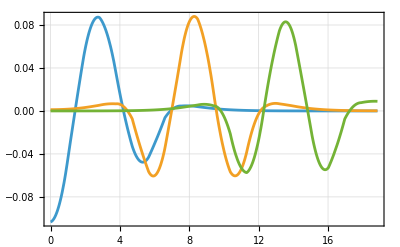

```mathematica
eig=Plot[{-eig1[[2,e1]][[1]],1.1eig2[[2,e2]][[1]],-1.05eig3[[2,e3]][[1]](*,0.75eig4[[2,e4]][[1]]*)},{x,0,xL},PlotRange->All,Frame->True,GridLines->Automatic]
```

#### Fitting sum of eigenfunctions

```mathematica
data = Table[Table[{x,asol[i, x]}, {x, 0, xL, xL/100}], {i, 5, 240, 5}];
```

```mathematica
nlm = Table[Join[{5i},{a, b,c} /. NonlinearModelFit[data[[i]], -a eig1[[2, e1]][[1]] + b 1.1  eig2[[2, e2]][[1]]-c eig3[[2,e3]][[1]], {a, b,c}, x]["BestFitParameters"]], {i, 1, Length[data]}];
```

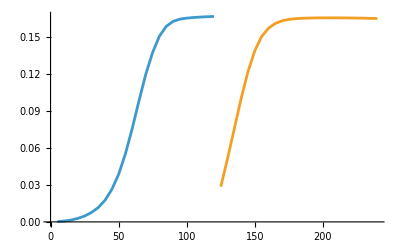

```mathematica
ListLinePlot[{nlm[[1;;24,{1,2}]],nlm[[25;;48,{1,3}]]}]
```

```mathematica
rsol=DSolve[{r'[t]==p1 r[t]-p2 r[t]^3,r[0]==r0},r[t],t,Assumptions->{r0>0,p1>0,p2>0}]//Quiet//FullSimplify;
```

```mathematica
functofit=r[t]/.rsol[[1,1]]
```

(ⅇ^(p1 t) √p1 r0)/(√(p1-p2 r0^2) √(1+(ⅇ^(2 p1 t) p2 r0^2)/(p1-p2 r0^2)))

```mathematica
nlmf = NonlinearModelFit[nlm[[1;;20, {1, 2}]], functofit, {{p1,0.1}, {p2,0.2}, {r0, 0.001}}, t]
```

FittedModel[…]

```mathematica
nlmf2 = NonlinearModelFit[nlm[[20;;40, {1, 3}]],functofit, {{p1,0.05}, {p2,0.4}, {r0, 0.001}}, t]
```

FittedModel[…]

```mathematica
nlmf["BestFitParameters"]
```

{p1→0.0752452,p2→2.74832,r0→0.000912387}

```mathematica
nlmf2["BestFitParameters"]
```

{p1→0.0900989,p2→3.37206,r0→4.03705×10^-7}

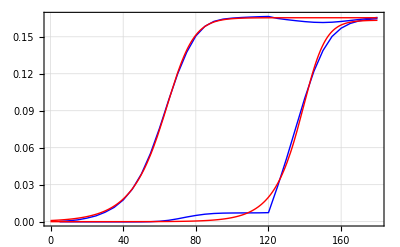

```mathematica
twopeaks120=Show[ListLinePlot[{nlm[[1;;36, {1, 2}]], nlm[[1;;36, {1, 3}]]},PlotStyle->{{Thick,Blue},{Thick,Blue}}], Plot[functofit/. nlmf["BestFitParameters"], {t, 0, 180},PlotStyle->{Thick,Red}], Plot[functofit/. nlmf2["BestFitParameters"], {t, 0, 180},PlotStyle->{Thick,Red}],Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

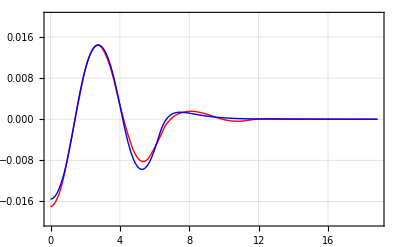

```mathematica
δ=110;
seq1=Plot[{-nlmf[δ]eig1[[2, e1]][[1]] + 1.2nlmf2[δ]eig2[[2, e2]][[1]], asol[δ, x]}, {x, 0, xL}, PlotRange -> {-0.02,0.02},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

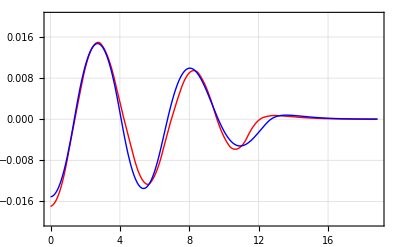

```mathematica
δ=140;
seq2=Plot[{-nlmf[δ]eig1[[2, e1]][[1]] + 1.12nlmf2[δ]eig2[[2, e2]][[1]], asol[δ, x]}, {x, 0, xL}, PlotRange -> {-0.02,0.02},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

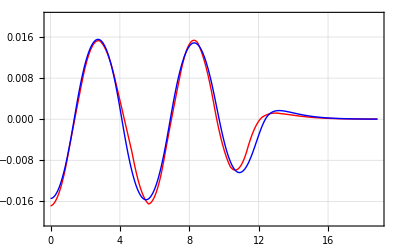

```mathematica
δ=180;
seq3=Plot[{-nlmf[δ]eig1[[2, e1]][[1]] + 1.12nlmf2[δ]eig2[[2, e2]][[1]], asol[δ, x]}, {x, 0, xL}, PlotRange -> {-0.02,0.02},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

#### For different timescales of the front/different period. Eigenfunctions remain the same, fitting changes. Period = 60

```mathematica
period=60;
```

```mathematica
eqn={1/τ D[a[t,x],{t,1}]==c[t,x]-ka a[t,x]+da D[a[t,x],{x,2}]-10a[t,x]^3,1/τ D[b[t,x],{t,1}]==c[t,x]-kb b[t,x]+db D[b[t,x],{x,2}]-b[t,x]^3,1/τ D[c[t,x],{t,1}]==α (1-f[x,t,period])a[t,x]+β b[t,x]+γ c[t,x]-c[t,x]^3+dc D[c[t,x],{x,2}]}/.eval;
```

```mathematica
ic={a[0,x]==0,b[0,x]==0.001(Sum[RandomReal[{0,1}]Cos[i x],{i,10}]),c[0,x]==0};
bc={Derivative[0,1][a][t,x0]==0,Derivative[0,1][a][t,xL]==0,Derivative[0,1][b][t,x0]==0,Derivative[0,1][b][t,xL]==0,Derivative[0,1][c][t,x0]==0,Derivative[0,1][c][t,xL]==0};
```

```mathematica
{asol,bsol,csol}=NDSolveValue[{eqn,ic,bc},{a,b,c},{t,0,T},{x,x0,xL}];
```

```mathematica
ListAnimate[Table[Plot[{asol[t,x],bsol[t,x](*,csol[t,x]*)},{x,x0,xL},PlotRange->{-0.04,0.04}],{t,0,T,10}]]
```

#### Fitting sum of eigenfunctions

```mathematica
data = Table[Table[{x, asol[i, x]}, {x, 0, xL, xL/100}], {i, 5, 240, 5}];
```

```mathematica
nlm = Table[Join[{5i},{a, b,c} /. NonlinearModelFit[data[[i]], -a eig1[[2, e1]][[1]] + b 1.1eig2[[2, e2]][[1]]+c eig3[[2,e3]][[1]], {a, b,c}, x]["BestFitParameters"]], {i, 1, Length[data]}];
```

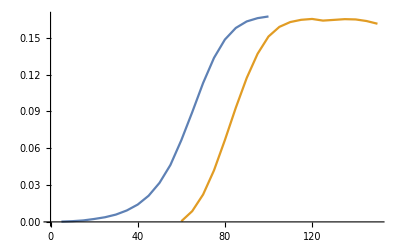

```mathematica
ListLinePlot[{nlm[[1;;20,{1,2}]],nlm[[12;;30,{1,3}]]}]
```

```mathematica
nlmf = NonlinearModelFit[nlm[[1;;25, {1, 2}]], functofit, {{p1,0.1}, {p2,0.2}, {r0, 0.001}}, t]
```

FittedModel[(«22» ⅇ^(«1»))/(√(1+«24» ⅇ^(«1»)))]

```mathematica
nlmf2 = NonlinearModelFit[nlm[[15;;30, {1, 3}]],functofit, {{p1,0.05}, {p2,0.4}, {r0, 0.001}}, t]
```

FittedModel[(«23» ⅇ^(«1»))/(√(1+«23» ⅇ^(«1»)))]

```mathematica
nlmf["BestFitParameters"]
```

{p1→0.0760411,p2→2.64845,r0→0.000733667}

```mathematica
nlmf2["BestFitParameters"]
```

{p1→0.0857539,p2→3.17595,r0→0.0000746252}

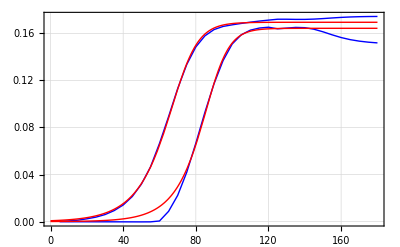

```mathematica
twopeaks60=Show[ListLinePlot[{nlm[[1;;36, {1, 2}]], nlm[[1;;36, {1, 3}]]},PlotStyle->{{Thick,Blue},{Thick,Blue}}], Plot[functofit/. nlmf["BestFitParameters"], {t, 0, 180},PlotStyle->{Thick,Red}], Plot[functofit/. nlmf2["BestFitParameters"], {t, 0, 180},PlotStyle->{Thick,Red}],Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

```mathematica
Export["seq_twopeaks60.pdf",twopeaks60]
```

seq_twopeaks60.pdf

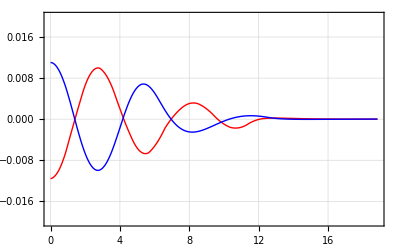

```mathematica
δ=70;
seq1=Plot[{-nlmf[δ]eig1[[2, e1]][[1]] + 1.12nlmf2[δ]eig2[[2, e2]][[1]], -asol[δ, x]}, {x, 0, xL}, PlotRange -> {-0.02,0.02},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

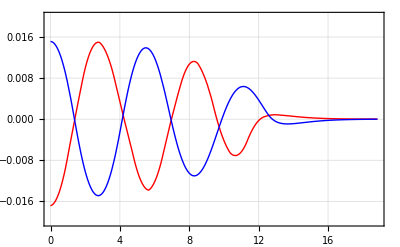

```mathematica
δ=90;
seq2=Plot[{-nlmf[δ]eig1[[2, e1]][[1]] + 1.12nlmf2[δ]eig2[[2, e2]][[1]], -asol[δ, x]}, {x, 0, xL}, PlotRange -> {-0.02,0.02},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

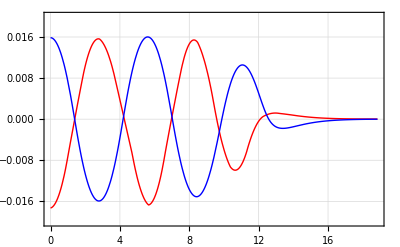

```mathematica
δ=120;
seq3=Plot[{-nlmf[δ]eig1[[2, e1]][[1]] + 1.12nlmf2[δ]eig2[[2, e2]][[1]], -asol[δ, x]}, {x, 0, xL}, PlotRange -> {-0.02,0.02},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

```mathematica
Export["seq_t60_2.pdf",seq2]
```

seq_t60_2.pdf

#### Dynamics with initial condition such that you get 3 and half peaks and then can fit with the same eigenfunctions?

```mathematica
τ=12;
T=400;
```

```mathematica
eqn={1/τ D[a[t,x],{t,1}]==c[t,x]-ka a[t,x]+da D[a[t,x],{x,2}]-10a[t,x]^3,1/τ D[b[t,x],{t,1}]==c[t,x]-kb b[t,x]+db D[b[t,x],{x,2}]-b[t,x]^3,1/τ D[c[t,x],{t,1}]==α (*(1-0f[x,t,period])*)a[t,x]+β b[t,x]+γ c[t,x]-c[t,x]^3+dc D[c[t,x],{x,2}]}/.eval;
```

```mathematica
ic={a[0,x]==0,b[0,x]==0.001(*(Sum[RandomReal[{0,1}]Cos[i x],{i,10}])*)Cos[7/6x],c[0,x]==0};
bc={Derivative[0,1][a][t,x0]==0,Derivative[0,1][a][t,xL]==0,Derivative[0,1][b][t,x0]==0,Derivative[0,1][b][t,xL]==0,Derivative[0,1][c][t,x0]==0,Derivative[0,1][c][t,xL]==0};
```

```mathematica
{asol,bsol,csol}=NDSolveValue[{eqn,ic,bc},{a,b,c},{t,0,T},{x,x0,xL},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->100,"MaxPoints"->300}}];
```

```mathematica
ListAnimate[Table[Plot[{-asol[t,x],-bsol[t,x](*,csol[t,x]*)},{x,x0,xL},PlotRange->{-0.04,0.04}],{t,0,T,10}]]
```

#### Fitting sum of eigenfunctions

```mathematica
data = Table[Table[{x, asol[i, x]}, {x, 0, xL, xL/100}], {i, 5, 240, 5}];
```

```mathematica
nlm = Table[Join[{5i},{a, b,c,d} /. NonlinearModelFit[data[[i]], a eig1[[2, e1]][[1]] - b 1.1eig2[[2, e2]][[1]]+1.05c eig3[[2,e3]][[1]]-0.75d eig4[[2,e4]][[1]], {a, b,c,d}, x]["BestFitParameters"]], {i, 1, Length[data]}];
```

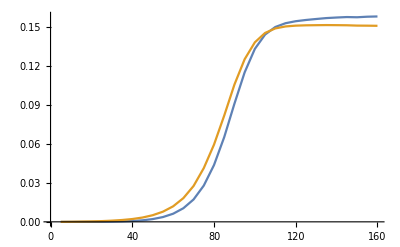

```mathematica
ListLinePlot[{nlm[[1;;32,{1,2}]],nlm[[1;;32,{1,3}]](*,nlm[[1;;32,{1,4}]],nlm[[1;;32,{1,5}]]*)}]
```

```mathematica
nlmf = NonlinearModelFit[nlm[[1;;40, {1, 2}]], functofit, {{p1,0.1}, {p2,0.2}, {r0, 0.001}}, t]
```

FittedModel[(«24» ⅇ^(«1»))/(√(1+«21» ⅇ^(«1»)))]

```mathematica
nlmf2 = NonlinearModelFit[nlm[[1;;40, {1, 3}]],functofit, {{p1,0.05}, {p2,0.4}, {r0, 0.001}}, t]
```

FittedModel[(«23» ⅇ^(«1»))/(√(1+«23» ⅇ^(«1»)))]

```mathematica
nlmf3 = NonlinearModelFit[nlm[[1;;40, {1, 4}]],functofit, {{p1,0.05}, {p2,0.4}, {r0, 0.001}}, t]
```

FittedModel[(«23» ⅇ^(«1»))/(√(1+«23» ⅇ^(«1»)))]

```mathematica
nlmf4 = NonlinearModelFit[nlm[[1;;40, {1, 5}]],functofit,{{p1,0.05}, {p2,0.4}, {r0, 0.001}}, t]
```

FittedModel[(«23» ⅇ^(«1»))/(√(1+«22» ⅇ^(«1»)))]

```mathematica
nlmf["BestFitParameters"]
nlmf2["BestFitParameters"]
nlmf3["BestFitParameters"]
nlmf4["BestFitParameters"]
```

{p1→0.0872656,p2→3.5182,r0→0.0000419707}

{p1→0.0834651,p2→3.65385,r0→0.0000811658}

{p1→0.0855805,p2→3.63969,r0→0.0000626211}

{p1→0.0891678,p2→3.71111,r0→0.0000321815}

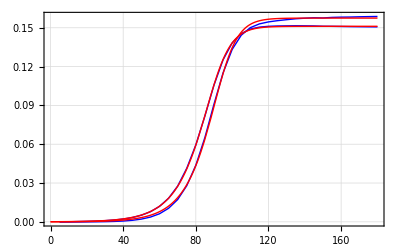

```mathematica
twopeaks1nofront=Show[ListLinePlot[{nlm[[1;;36, {1, 2}]], nlm[[1;;36, {1, 3}]](*,nlm[[1;;32, {1, 4}]]*)},PlotStyle->{{Thick,Blue},{Thick,Blue}}], Plot[functofit/. nlmf["BestFitParameters"], {t, 0, 180},PlotStyle->{Thick,Red}], Plot[functofit/. nlmf2["BestFitParameters"], {t, 0, 180},PlotStyle->{Thick,Red}],(*Plot[functofit/. nlmf3["BestFitParameters"], {t, 0, 200},PlotStyle->{Thick,Red}],*)Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

```mathematica
Export["twopeaks_nofront.pdf",twopeaks1nofront]
```

twopeaks_nofront.pdf

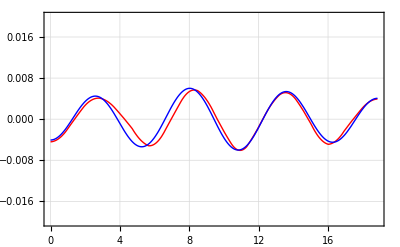

```mathematica
δ=80;
seq1=Plot[{-nlmf[δ]eig1[[2, e1]][[1]] + 1.1nlmf2[δ]eig2[[2, e2]][[1]]-1.05nlmf3[δ]eig3[[2, e3]][[1]]+0.75nlmf4[δ]eig4[[2, e4]][[1]], -asol[δ, x]}, {x, 0, xL}, PlotRange -> {-0.02,0.02},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

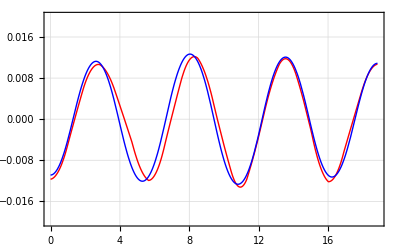

```mathematica
δ=95;
seq2=Plot[{-nlmf[δ]eig1[[2, e1]][[1]] + 1.1nlmf2[δ]eig2[[2, e2]][[1]]-1.05nlmf3[δ]eig3[[2, e3]][[1]]+0.75nlmf4[δ]eig4[[2, e4]][[1]], -asol[δ, x]}, {x, 0, xL}, PlotRange -> {-0.02,0.02},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

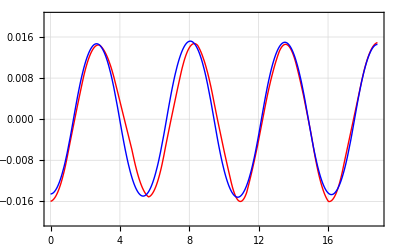

```mathematica
δ=120;
seq3=Plot[{-nlmf[δ]eig1[[2, e1]][[1]] + 1.1nlmf2[δ]eig2[[2, e2]][[1]]-1.05nlmf3[δ]eig3[[2, e3]][[1]]+0.75nlmf4[δ]eig4[[2, e4]][[1]], -asol[δ, x]}, {x, 0, xL}, PlotRange -> {-0.02,0.02},PlotStyle->{{Thick,Red},{Thick,Blue}},Frame->True,GridLines->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman",14}]
```

```mathematica
Export["nofront_2.pdf",seq2]
```

nofront_2.pdf